# Chapter 3: Integration

## The application of physical laws-given for mathematical points-to ex-tended everyday objects requires integration, the subject of this chapter. We shall consider various examples from selected branches of physics.

## Integration in Mathematica

```mathematica
?Integrate
```

```mathematica
?NIntegrate
```

Let’s start our discussion with the example of a simple pendulum

The general formula for T is   4 √(l/g)∫_0^(π/2) 1/(√(1-sin^2(θ/2)sin^2 u))ⅆu

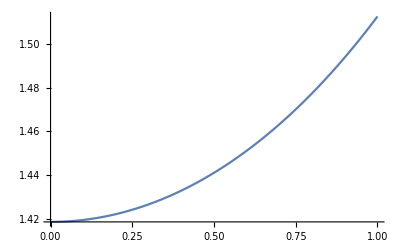

```mathematica
g=9.81;
t[theta_,l_]:=4 Sqrt[l/g]Integrate[1/Sqrt[1-(Sin[theta/2] Sin[u])^2],{u,0,Pi/2}]

Plot[Evaluate[t[tv,0.5]],{tv,0,1}]
```

## Integration in Mechanics

∫_v0^v uⅆu = 1/m ∫_x0^x f(s)ⅆs ; Position dependent force 

t  = ∫_x0^x 1/(√(v0^2+2/m∫_x0^x f(s)ⅆs))ⅆx this equation cannot be solved analytically so we will use the numerical way to solve it.

```mathematica
(*Step 1:Force function*)
f[s_]:=s

(*Step 2:Integral of force*)
F[x_,x0_]:=Integrate[f[s],{s,x0,x}]

(*Step 3:Function g*)
g[x_,x0_,v0_]:=Integrate[1/Sqrt[v0^2+F[u,x0]],{u,x0,x}]

(*Step 4:Solve g[x,1,1]==1*)
FindRoot[g[x,1,1]-1,{x,1}]
```

{x→2.34603}